# Dynamical Systems and Chaos

## Language competition Pablo Rosillo

Code used for simulations in the Language Competition project. 

Firstly, simulations of Louf et al. model depending on parameters.

## Louf et al. eqs.

```mathematica
mu = 0.02;
xeq = mu*(1-x-y)*s*(x+q*(1-x-y))-c*(1-mu)*x*(1-s)*(y+(1-q)*(1-x-y));
yeq = mu*(1-x-y)*(1-s)*(y+(1-q)*(1-x-y))-c*(1-mu)*y*s*(x+q*(1-x-y));
genericEigen = Eigenvalues[{
{D[xeq, x], D[xeq, y]},
{D[yeq, x], D[yeq, y]}
}];
```

## Louf et al. vector field

```mathematica
texMathStyle={FontFamily->"CMU Serif",FontSize->7*1.5};
texTextStyle = {FontFamily-> "Latin Modern Roman", FontSize->7*1.5} ;
cm=1.38095*72/2.54;
```

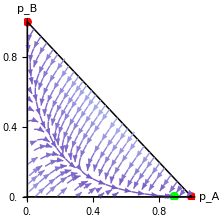

/Users/pablorosillo/Library/CloudStorage/OneDrive-UniversitatdelesIllesBalears/Máster IFISC/Asignaturas/Dynamical Systems/Final project/Códigos Pablo/figs3basic/louf_stream_plot_eq_mu=0.02_s=0.57_q=0.45_c=0.05.pdf

```mathematica
numTol = 10^(-10);
(* Parameters chosen for the simulation. These may vary from one figure to another to
represent different situations. *)
params = {s->0.57, q->0.45, c->0.05};
(* Solution limited to Reals and not only positive ones because the result will be numericised by
Mathematica, and there can be a floating point accuracy error making zero solutions negative *)
plotSol = Solve[{xeq==0, yeq==0}/.params, {x, y},Reals];
plotEigen = Re[genericEigen /.params/.plotSol];
valuesSol =  Normal @Table[{x,y}/.plotSol[[i]], {i, 1, Length[plotSol]}];
validIdx = Flatten[Position[
valuesSol,
_?(#[[1]]≥ -numTol && #[[2]]≥ -numTol && #[[1]]+#[[2]]≤ 1+numTol&)]];
stableIdx = Position[plotEigen[[validIdx]], _?(NumericQ[#[[1]]]&& NumericQ[#[[2]]]&& #[[1]] < 0 &&  #[[2]] < 0 &)];
(* Delete cannot take the flattened version because otherwise it deletes an element going in higher dimension. 
 If there is either no stable or unstable solution, we need to replace the corresponding empty list by ∅, 
   because ListPlot can't handle an empty list correctly. *)
p1 = ListPlot[
{valuesSol[[validIdx]][[Flatten[stableIdx]]], Delete[valuesSol[[validIdx]], stableIdx]}/.{}->{∅}, PlotStyle->{Directive[PointSize[0.03], Green], Directive[PointSize[0.03],Red]}];
p2 = StreamPlot[
{xeq, yeq}/.params, {x,0,1}, {y, 0,1},
RegionFunction->Function[{x,y},x+y≤1 &&x≥0 && y≥ 0],
 StreamColorFunction-> "Blue",
RegionFillingStyle->None, RegionBoundaryStyle->Directive[Black, Thickness[0.005]]];
plot = Show[p1, p2, PlotRange->{{0,1}, {0,1}}, AspectRatio->Automatic, AxesLabel->{Subscript[p, A],Subscript[p, B]}, BaseStyle->texMathStyle,
Ticks->{{#,Framed[#,FrameMargins->-1,FrameStyle->None]}&/@Range[0,1,0.2],{#,Framed[#,FrameStyle->None]}&/@Range[0,1,0.2]},
 ImageSize-> {5.6cm,5.6cm}]
paramsStr ="_mu="<>ToString[mu]<>"_s="<>ToString[s/.params]<>"_q="<>ToString[q/.params]<> "_c="<>ToString[c/.params];
fileName = FileNameJoin[{NotebookDirectory[],"figs3basic", "louf_stream_plot_eq"<>paramsStr<>".pdf"}]
Export[fileName,plot, Magnification->1] ;
```

Secondly, simulation of Castelló et al. model, with the same method as Louf et al. model.

## Castelló et al. general eqs.

```mathematica
xeqcg[x_, y_] = (1-x-y)*s*(1-y)^a -x*y^a*(1-s);
yeqcg[x_, y_] = (1-s)*(1-x)^a*(1-x-y)-s*x^a *y;
```

## Castelló et al. general vector field

```mathematica
paramscg = {a -> 0.5, s -> 0.5}
points = Solve[{0 == xeqcg[x,y]/.paramscg, 0 == yeqcg[x,y] /. paramscg}, {x,y} , Reals]
```

{a→0.5,s→0.5}

{{x→0,y→1.},{x→0.362993,y→0.362993},{x→1.,y→0}}

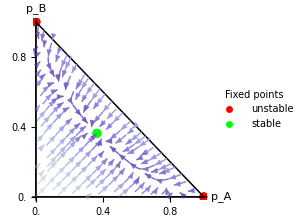

/Users/pablorosillo/Library/CloudStorage/OneDrive-UniversitatdelesIllesBalears/Máster IFISC/Asignaturas/Dynamical Systems/Final project/Códigos Pablo/figs/castellogeneral_stream_plot_eq_a=0.5_s=0.5.pdf

```mathematica
datapre = Transpose[{{1, 0.3629925249502724, 0},{0, 0.3629925249502715, 1}}];
data={#}&/@datapre;
p2 = StreamPlot[{xeqcg[x,y], yeqcg[x,y]} /. paramscg, {x, 0, 1}, {y, 0, 1}, RegionFunction->Function[{x,y},x+y≤1 &&x≥0 && y≥ 0], StreamColorFunction-> "Blue",RegionFillingStyle->None, RegionBoundaryStyle->Directive[Black, Thickness[0.005]]];
p1 = ListPlot[data, PlotStyle->{Directive[PointSize[0.03],Red], Directive[PointSize[0.03],Green], Directive[PointSize[0.03],Red]}, PlotLegends->Placed[PointLegend[{"unstable", "stable"},LegendLabel->"Fixed points", LabelStyle->texMathStyle, LegendMarkerSize->6],
{Scaled[{0.8,0.95}], {1, 1}}]];
texMathStyle={FontFamily->"CMU Serif",FontSize->7*1.5};
texTextStyle = {FontFamily-> "Latin Modern Roman", FontSize->7*1.5} ;
cm=1.38095*72/2.54;
plot = Show[p1, p2, PlotRange->{{0,1}, {0,1}}, AspectRatio->Automatic, AxesLabel->{Subscript[p, A],Subscript[p, B]}, BaseStyle->texMathStyle,
Ticks->{{#,Framed[#,FrameMargins->-1,FrameStyle->None]}&/@Range[0,1,0.2],{#,Framed[#,FrameStyle->None]}&/@Range[0,1,0.2]},
 ImageSize-> {5.6cm,5.6cm}]
paramsStr ="_a="<>ToString[a/.paramscg]<>"_s="<>ToString[s/.paramscg];
fileName = FileNameJoin[{NotebookDirectory[],"figs", "castellogeneral_stream_plot_eq"<>paramsStr<>".pdf"}]
Export[fileName,plot, Magnification->1] ;
```

```mathematica
paramscg = {a -> 1, s -> 0.5}
points = NSolve[{0 == xeqcg[x,y]/.paramscg, 0 == yeqcg[x,y] /. paramscg}, {x,y} , Reals]
```

{a→1,s→0.5}

{{x→2.61803,y→2.61803},{x→1.,y→0.},{x→0.,y→1.},{x→0.381966,y→0.381966}}

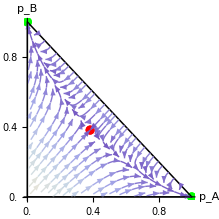

/Users/pablorosillo/Library/CloudStorage/OneDrive-UniversitatdelesIllesBalears/Máster IFISC/Asignaturas/Dynamical Systems/Final project/Códigos Pablo/figs/castellogeneral_stream_plot_eq_a=1_s=0.5.pdf

```mathematica
datapre = Transpose[{{1, 0, 0.3819660112501088},{0, 1, 0.3819660112500995}}];
data={#}&/@datapre;
p2 = StreamPlot[{xeqcg[x,y], yeqcg[x,y]} /. paramscg, {x, 0, 1}, {y, 0, 1}, RegionFunction->Function[{x,y},x+y≤1 &&x≥0 && y≥ 0], StreamColorFunction-> "Blue",RegionFillingStyle->None, RegionBoundaryStyle->Directive[Black, Thickness[0.005]]];
p1 = ListPlot[data, PlotStyle->{Directive[PointSize[0.03],Green], Directive[PointSize[0.03],Green], Directive[PointSize[0.03],Red]}];
texMathStyle={FontFamily->"CMU Serif",FontSize->7*1.5};
texTextStyle = {FontFamily-> "Latin Modern Roman", FontSize->7*1.5} ;
cm=1.38095*72/2.54;
plot = Show[p1, p2, PlotRange->{{0,1}, {0,1}}, AspectRatio->Automatic, AxesLabel->{Subscript[p, A],Subscript[p, B]}, BaseStyle->texMathStyle,
Ticks->{{#,Framed[#,FrameMargins->-1,FrameStyle->None]}&/@Range[0,1,0.2],{#,Framed[#,FrameStyle->None]}&/@Range[0,1,0.2]},
 ImageSize-> {5.6cm,5.6cm}]
paramsStr ="_a="<>ToString[a/.paramscg]<>"_s="<>ToString[s/.paramscg];
fileName = FileNameJoin[{NotebookDirectory[],"figs", "castellogeneral_stream_plot_eq"<>paramsStr<>".pdf"}]
Export[fileName,plot, Magnification->1] ;
```

```mathematica
paramscg = {a -> 2, s -> 0.1}
points = NSolve[{0 == xeqcg[x,y]/.paramscg, 0 == yeqcg[x,y] /. paramscg}, {x,y} , Reals]
```

{a→2,s→0.1}

{{x→1.,y→0.},{x→0.754517,y→0.119767},{x→0.,y→1.}}

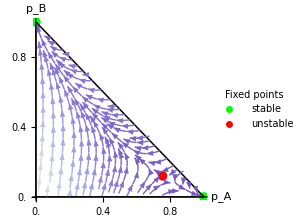

/Users/pablorosillo/Library/CloudStorage/OneDrive-UniversitatdelesIllesBalears/Máster IFISC/Asignaturas/Dynamical Systems/Final project/Códigos Pablo/figs/castellogeneral_stream_plot_eq_a=2_s=0.1.pdf

```mathematica
datapre = Transpose[{{1, 0.7545171225278263, 0},{0, 0.11976695483563915, 1}}];
data={#}&/@datapre;
p2 = StreamPlot[{xeqcg[x,y], yeqcg[x,y]} /. paramscg, {x, 0, 1}, {y, 0, 1}, RegionFunction->Function[{x,y},x+y≤1 &&x≥0 && y≥ 0], StreamColorFunction-> "Blue",RegionFillingStyle->None, RegionBoundaryStyle->Directive[Black, Thickness[0.005]]];
p1 = ListPlot[data, PlotStyle->{Directive[PointSize[0.03],Green], Directive[PointSize[0.03],Red], Directive[PointSize[0.03],Green]}, PlotLegends->Placed[PointLegend[{"stable", "unstable"},LegendLabel->"Fixed points", LabelStyle->texMathStyle, LegendMarkerSize->6],
{Scaled[{0.8,0.95}], {1, 1}}]];
texMathStyle={FontFamily->"CMU Serif",FontSize->7*1.5};
texTextStyle = {FontFamily-> "Latin Modern Roman", FontSize->7*1.5} ;
cm=1.38095*72/2.54;
plot = Show[p1, p2, PlotRange->{{0,1}, {0,1}}, AspectRatio->Automatic, AxesLabel->{Subscript[p, A],Subscript[p, B]}, BaseStyle->texMathStyle,
Ticks->{{#,Framed[#,FrameMargins->-1,FrameStyle->None]}&/@Range[0,1,0.2],{#,Framed[#,FrameStyle->None]}&/@Range[0,1,0.2]},
 ImageSize-> {5.6cm,5.6cm}]
paramsStr ="_a="<>ToString[a/.paramscg]<>"_s="<>ToString[s/.paramscg];
fileName = FileNameJoin[{NotebookDirectory[],"figs", "castellogeneral_stream_plot_eq"<>paramsStr<>".pdf"}]
Export[fileName,plot, Magnification->1] ;
```